Logic

Predicate Logic

### Overview

Predicate logic expands the range of propositions that are possible.

A particular form of programming is possible using predicate logic: logic programming.

Universal truths can be differentiated from special cases.

You will learn about predicates and quantifiers.

-Graphics-

### Predicates

Many propositions have variables that determine their value.

The melting point of x element is y Kelvin:

```mathematica
M[x,y]
```

Popular predicates include equality predicates, namely <, >, ≤ (<=), ≥ (>=), = (==) and ≠ (!=):

```mathematica
(x+2>4)⇒(x+3<4)
```

2+x>4⇒3+x<4

```mathematica
{%/.x->2,%/.x->3}
```

{True,False}

### Example

Consider the proposition:

```mathematica
p=x^2+y^2==z^2
```

x^2+y^2==z^2

What is the truth value for x=5, y=12 and z=13?

```mathematica
p/.{x->5,y->12,z->13}
```

True

What is the truth value for x=160, y=241 and z=290?

```mathematica
p/.{x->160,y->241,z->290}
```

False

To learn more about this equation, read about Pythagorean triples.

### Universal Quantifier ∀

Universal quantification is the proposition: “P(x) is true for all values of x.”

∀x (x^2>=0)

```mathematica
ForAll[x,x^2>=0]
```

∀_x x^2≥0

∀x>=2 (x>=0)

```mathematica
ForAll[x,x>=2,x>=0]
```

∀_(x,x≥2)x≥0

```mathematica
Reduce[%]
```

True

### Existential Quantifier ∃

Existential quantification is the proposition: “P(x) is true for at least one value of x.”

∃x (x==-x)

```mathematica
Exists[x,x==-x]
```

∃_x x==-x

This is a special case of existence. It is unique and is denoted by ∃!x.

∃x,y (x^2+ay^2<=1∧x-y≥2)

```mathematica
Exists[{x,y},x^2+a y^2<=1&&x-y>=2]
```

∃_{x,y}(x^2+a y^2≤1&&x-y≥2)

```mathematica
Reduce[%,a]
```

a≤1/3

### Example

Test whether one region is included in another:

```mathematica
R1=(2 x)^2+y^2+2 x y<=1;
R2=x^2+y^2<=2;
```

```mathematica
Exists[{x,y},R1&&!R2]//Reduce
```

False

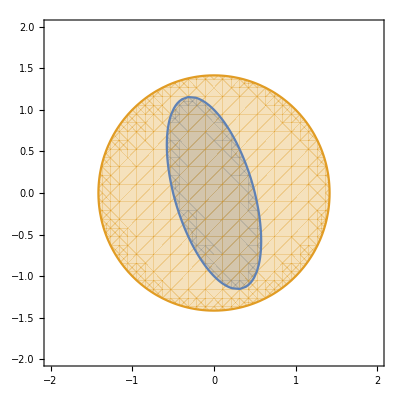

```mathematica
Show@RegionPlot[{R1,R2},{x,-2,2},{y,-2,2}]
```

### Equivalences

Equivalences are also used for quantifiers, using Resolve or Reduce:

```mathematica
Grid[{{"Conjuction","∀x(P(x)∧Q(x))⧦∀x P(x)∧ ∀x Q(x)"},{"Disjunction","∃x(P(x)∨Q(x))⧦∃x P(x)∨ ∃x Q(x)"},{"De Morgan's for ∀","¬∀x P(x)⧦∃x(¬P(x))"},{"De Morgan's for ∃","¬∃x P(x)⧦∀x(¬P(x))"}},Frame->All]
```

Conjuction | ∀x(P(x)∧Q(x))⧦∀x P(x)∧ ∀x Q(x)
Disjunction | ∃x(P(x)∨Q(x))⧦∃x P(x)∨ ∃x Q(x)
De Morgan's for ∀ | ¬∀x P(x)⧦∃x(¬P(x))
De Morgan's for ∃ | ¬∃x P(x)⧦∀x(¬P(x))

In fact, the negative can be passed all the way down the expression:

¬∃v ∀w∃x∃y∀z P(v,w,x,y,z)

∀v ¬∀w∃x∃y∀z P(v,w,x,y,z)

∀v ∃w¬∃x∃y∀z P(v,w,x,y,z)

∀v ∃w∀x∀y∃z ¬P(v,w,x,y,z)

### Nested Quantifiers

How to interpret nested quantifiers:

```mathematica
Grid[{{"∃x∃y P(x)","At least one pair exists."},{"∀x∃y P(x)","A pair exists for every x"},{"∃x ∀y P(x)","A pair with a specific x & any y"},{"∀x ∀y P(x)","All pairs work!"}},Frame->All]
```

∃x∃y P(x) | At least one pair exists.
∀x∃y P(x) | A pair exists for every x
∃x ∀y P(x) | A pair with a specific x & any y
∀x ∀y P(x) | All pairs work!

Everyone in this course likes a branch of mathematics:

∀s∈students∃b∈mathematics(Likes(s,b))

### Examples

Translate the following statements in logic:

No one is perfect.

¬∃x(Perfect(x))

Not all propositions are contradictions.

¬∀x(Contradiction(x))

In my second-year class, only one person knew Java, SQL and Python.

∃!x(Java(x)∧SQL(x)∧Python(x))

### Summary

Predicates are propositional functions with parameters.

There are three quantifiers: Universal (ForAll, ∀), Existence (Exists, ∃) and Uniqueness (∃!).

Simplifications are possible through Resolve or Reduce.

So far, propositions were taken as is.

The next lesson allows for analysis of propositions through rules of inference.

Download Notebook »